```mathematica
xzawed'
```

```mathematica
39 2 4 5 9 12
```

```mathematica
2.
```

```mathematica
Solve[{(0.3+a)(a+b)==a,0.3+a+b+0.2==1},{a,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.3,b→0.2}}

```mathematica
4.
```

```mathematica
TableForm[{{0.2,0.0},{0.1,0.4},{0.1,0.2}},TableHeadings->{{0,1,2},{0,1}}]
```

| 0 | 1
0 | 0.2 | 0.
1 | 0.1 | 0.4
2 | 0.1 | 0.2

```mathematica
{0.2,0.1,0.1}*(1/0.4)
```

{0.5,0.25,0.25}

```mathematica
{#1,#2/Length[{First[#],Max[#]}&/@Tuples[{Range[6],Range[6]}]]}&@@@Tally[{First[#],Max[#]}&/@Tuples[{Range[6],Range[6]}]]
```

{{{1,1},1/36},{{1,2},1/36},{{1,3},1/36},{{1,4},1/36},{{1,5},1/36},{{1,6},1/36},{{2,2},1/18},{{2,3},1/36},{{2,4},1/36},{{2,5},1/36},{{2,6},1/36},{{3,3},1/12},{{3,4},1/36},{{3,5},1/36},{{3,6},1/36},{{4,4},1/9},{{4,5},1/36},{{4,6},1/36},{{5,5},5/36},{{5,6},1/36},{{6,6},1/6}}

```mathematica
Total[%255]
```

{{56,91},1}

```mathematica
Select[{#1,#2/Length[{First[#],Max[#]}&/@Tuples[{Range[6],Range[6]}]]}&@@@Tally[{First[#],Max[#]}&/@Tuples[{Range[6],Range[6]}]],#2==6&@@Flatten[#]&]
```

{{{1,6},1/36},{{2,6},1/36},{{3,6},1/36},{{4,6},1/36},{{5,6},1/36},{{6,6},1/6}}

```mathematica
Total[%266]
```

{{21,36},11/36}

```mathematica
9.
```

```mathematica
TableForm[Transpose[{{0.1,0.3},{0.2,0.4}}],TableHeadings->{{"X=1",2},{"Y=0",1}}]
```

| Y=0 | 1
X=1 | 0.1 | 0.2
2 | 0.3 | 0.4

```mathematica
Solve[Integrate[Integrate[c(y-x),{y,x,1}],{x,0,1}]==1,c]
```

{{c→6}}

```mathematica
Integrate[Integrate[6(y-x),{y,x,1-x}],{x,0,0.5}]
```

0.5

```mathematica
Integrate[Integrate[6(y-x),{y,x,1}],{x,0,0.5}]
```

0.875

```mathematica
Clear[f,X];
f[x_]:=PDF[NormalDistribution[0,1],x];
D[Integrate[f[x],{x,-Infinity,Log[x]}],x]
```

(ⅇ^(-1/2 Log[x]^2))/(√(2 π) x)

```mathematica
TraditionalForm@D[Integrate[f[x],{x,-Exp[x],Exp[x]}],x]
```

√(2/π) ⅇ^(x-ⅇ^(2 x)/2)

```mathematica
f[x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
15 16 20 24 28
```

```mathematica
15.
```

```mathematica
Integrate[E^-x,{y,0,x}]
```

ⅇ^-x x

```mathematica
Integrate[E^-x,{x,y,Infinity}]
```

ⅇ^-y

```mathematica
1/x
```

1+y

```mathematica
好像是的吧。
```

```mathematica
16.
```

```mathematica
λ^2 E^(-λ x) E^(-y/x)(x>0,y>0)
```

```mathematica
Integrate[Integrate[λ^2 E^(-λ x) E^(-y/x),{y,0,Infinity}],{x,0,Infinity}]
```

Piecewise[{{1, Re[λ]>0}, {Integrate[ConditionalExpression[ⅇ^(-x λ) x λ^2,Re[x]>0],{x,0,∞},Assumptions→Re[λ]≤0], True}}]

```mathematica
Integrate[1/x Exp[-y/x],{y,0,y}]
```

1-ⅇ^(-y/x)

```mathematica
Integrate[1/x Exp[-y/x]/.x->1,{y,1,Infinity}]
```

1/ⅇ

```mathematica
N@%
```

0.367879

```mathematica
20.
```

f_z=2/m^2(0<z<2x,0<x<1/2 m)
		=1/m^2(2x<z<m,0<x<1/2 m)
		=1/m^2(0<z<2x-m,m/2<x<m)
		=2/m^2(2x-m<z<m,m/2<x<m)

```mathematica
24.
```

```mathematica
(1-(1-#)*(1-#))*#&[Integrate[ⅇ^(-x λ) λ,{x,x,Infinity}]]
```

ConditionalExpression[ⅇ^(-x λ) (1-(1-ⅇ^(-x λ))^2),Re[λ]>0]

```mathematica
Integrate[ⅇ^(-x λ) (1-(1-ⅇ^(-x λ))^2),{x,0,Infinity}]
```

ConditionalExpression[2/(3 λ),Re[λ]>0]

```mathematica
Integrate[Integrate[Integrate[ⅇ^(-(x1+x2+x3) λ) λ^3,{x3,T,Infinity}],{x2,0,Infinity}],{x1,0,Infinity}]-Integrate[Integrate[Integrate[ⅇ^(-(x1+x2+x3) λ) λ^3,{x3,T,Infinity}],{x2,0,T}],{x1,0,T}]
```

ConditionalExpression[ⅇ^(-T λ)-ⅇ^(-3 T λ) (-1+ⅇ^(T λ))^2,Re[λ]>0]

```mathematica
Simplify[-D[ⅇ^(-T λ)-ⅇ^(-3 T λ) (-1+ⅇ^(T λ))^2,T]](*密度函数*)
```

ⅇ^(-3 T λ) (-3+4 ⅇ^(T λ)) λ

```mathematica
Integrate[-D[ⅇ^(-T λ)-ⅇ^(-3 T λ) (-1+ⅇ^(T λ))^2,T],{T,0,t}](*分布函数*)
```

1+ⅇ^(-3 t λ)-2 ⅇ^(-2 t λ)

```mathematica
29.
```

```mathematica
(0.5/2+1)/2
```

0.625

```mathematica
1/32.4(x-48)(48<x<60)
```

```mathematica
1/16.2(x-54) (60<x<64)
1/32.4(x-80)+1(64<x<80)
```

0.37037+0.0617284 (-60+x)

```mathematica
Solve[{k1 *48+b1==0,k1*60+b1==2k1*60+b2,2k1*64+b2==k1*64+b3,k1*80+b3==1},{k1,b1,b2,b3}]
```

{{k1→1/36,b1→-4/3,b2→-3,b3→-11/9}}

-----------------------------

```mathematica
list=Table[Median[Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},100]],100000];
Histogram[list,{0,01},"Probability"]
```

Histogram::hbins: The bin specification {0,1} cannot be used to determine either how many or which bins to use.

Histogram[{0.463665,0.793518,0.137572,0.712516,0.206199,99991,0.512353,0.286861,0.599586,0.156168},{1},Probability]
 |  |  |  |

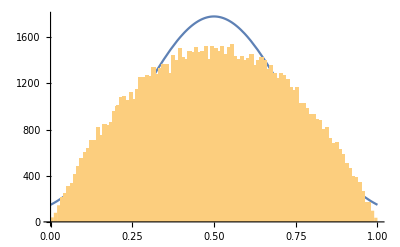

```mathematica
Show[Plot[(PDF[NormalDistribution[0.5,StandardDeviation[list]],x])*1000,{x,0,1}],Histogram[list,{0.01}]]
```

```mathematica
Integrate[PDF[NormalDistribution[0.5,StandardDeviation[list]],x],{x,0,1}]
```

0.974341

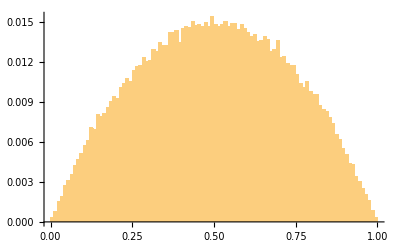

```mathematica
Histogram[list,{0.01},"Probability"]
```

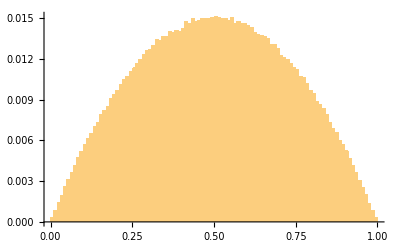

```mathematica
list=Table[Median[Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},100]],1000000];
Histogram[list,{0.01},"Probability"]
```

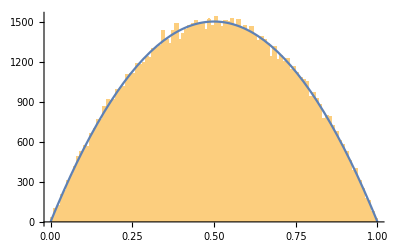

```mathematica
Show[Histogram[list,{0.01}],Plot[-6000x(x-1),{x,0,1}]]
```

```mathematica
Integrate[Sqrt[x]Log[x]/(x^2+1),{x,0,Infinity}]
```

π^2/(2 √2)

```mathematica
Solve[Integrate[a*x(x-1),{x,0,1}]==1,a]
```

{{a→-6}}

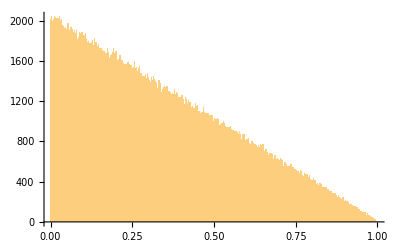

```mathematica
Histogram[Table[Abs[RandomReal[{0,1}]-RandomReal[{0,1}]],1000000],{0.001}]
```

```mathematica
Integrate[m-z,{z,0,m}]
```

m^2/2

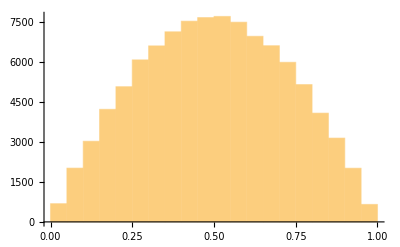
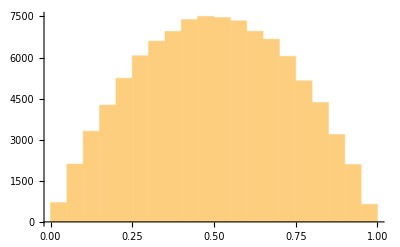
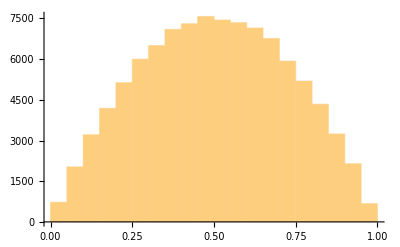
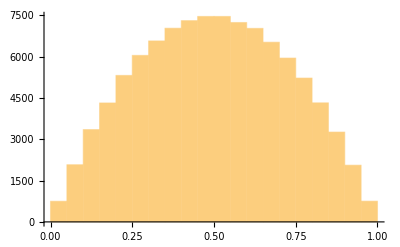
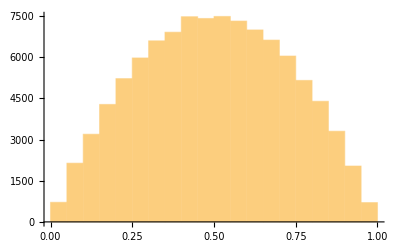
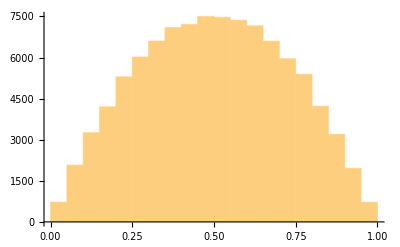
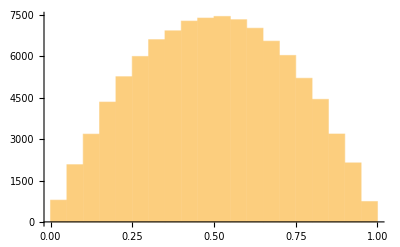
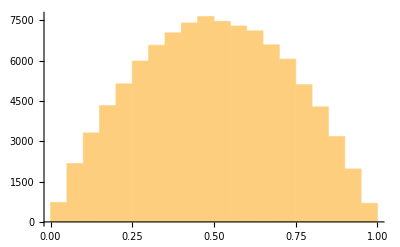

```mathematica
Table[Histogram[Table[Median[Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},i]],100000]],{i,1,10}]
```

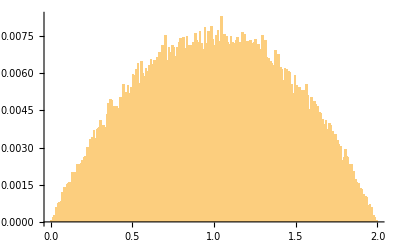

```mathematica
list=Table[Median[Nest[Table[RandomReal[#],2]&,{RandomReal[{0,2}],RandomReal[{0,2}]},100]],100000];
Histogram[list,{0.01},"Probability"]
```

```mathematica
list=Table[Max[Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},100]],100000];
```

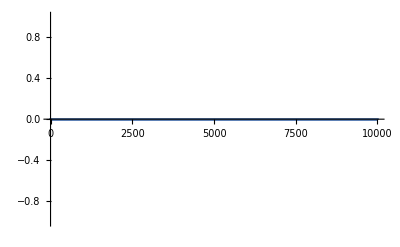

```mathematica
ListPlot[Table[Abs[Subtract@@(Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},100])],10000]]
```

```mathematica
Subtract@@Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},100]
```

0.

```mathematica
DSolveValue[y'[x]+y[x]==a Sin[x],y[x],x]
```

ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])

```mathematica
DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

```mathematica
list=Table[Median[Nest[Table[RandomReal[#],2]&,{RandomReal[],RandomReal[]},100]],100000];
Histogram[list,{0,01},"Probability"]
```

Histogram::hbins: The bin specification {0,1} cannot be used to determine either how many or which bins to use.

Histogram[1]
 |  |  |  |

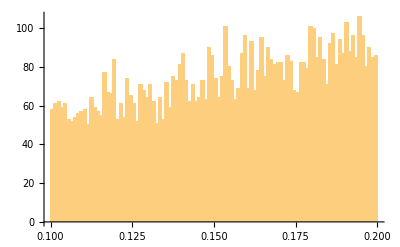

```mathematica
Histogram[Select[list,0.1<#<0.2&],{0.001}]
```

```mathematica
Integrate[6(1-x)x,{x,0,a}]
```

3 a^2-2 a^3

```mathematica
Integrate[6x(1-x),{x,0,1}]
```

1

```mathematica
CDF[BetaDistribution[2,2],x]
```

Piecewise[{{BetaRegularized[x,2,2], 0<x<1}, {1, x≥1}, {0, True}}]

```mathematica
BetaRegularized[x,2,2]
```

BetaRegularized[x,2,2]

```mathematica
Integrate[6x(1-x),{x,0,x}]/.x->0.5
```

0.5

```mathematica
f[x_]:=Integrate[6x(1-x),{x,0,x}];
x^2+1/2 Integrate[f[x],{x,0,1}]-Integrate[Integrate[L*f[x],{x,x/L,1}],{L,x,1}]-Integrate[Integrate[L*f[x],{x,0,(x+L-1)/L}],{L,1-x,1}]
```

ConditionalExpression[1/4+x^2-x^4/4+1/4 (-1+x)^2 (-1+(-2+x) x),((Re[x/(1-x)]≥0&&x/(-1+x)≠0)||x/(1-x)∉Reals||Re[x/(1-x)]<-1)&&(x∉Reals||Re[x]>1||0<Re[x]<1)&&(Re[x]≤1||x∉Reals)]

```mathematica
Clear[f];
```

```mathematica
DSolve[{f[x]==x^2+1/2 Integrate[f[x],{x,0,1}]-Integrate[Integrate[L*f[x],{x,x/L,1}],{L,x,1}]-Integrate[Integrate[L*f[x],{x,0,(x+L-1)/L}],{L,1-x,1}],f[0]==0,f[1/2]==1/2},f[x],{x,0,0.5}]
```

DSolve[{f[x]==x^2+1/2 ∫_0^1 f[x]ⅆx-∫_(1-x)^1 (∫_0^((-1+L+x)/L) L f[x]ⅆx)ⅆL-∫_x^1 (∫_(x/L)^1 L f[x]ⅆx)ⅆL,f[0]==0,f[1/2]==1/2},f[x],{x,0,0.5}]

```mathematica
Simplify[1/4+x^2-x^4/4+1/4 (-1+x)^2 (-1+(-2+x) x)]
```

-(-2+x) x^2

```mathematica
D[x^2+1/2 Integrate[f[x],{x,0,1}]-Integrate[Integrate[L*f[x],{x,x/L,1}],{L,x,1}]-Integrate[Integrate[L*f[x],{x,0,(x+L-1)/L}],{L,1-x,1}],x]
```

2 x-∫_x^1 -f[x/L]ⅆL-∫_(1-x)^1 f[(-1+L+x)/L]ⅆL

```mathematica
DSolve[f'[x]==2 x-∫_x^1 -f[x/L]ⅆL-∫_(1-x)^1 f[(-1+L+x)/L]ⅆL,f[x],x]
```

$Aborted

```mathematica
DSolve[{f'[x]==Integrate[x^2/s^3 f[s],{s,x,1}]-Integrate[(x-1)^2/(s-1)^3 f[s],{s,0,x}],f[0]==0},f[x],x]
```

{{f[x]→-∫_1^0 -∫_0^K[1] (f[s] (-1+K[1])^2)/(-1+s)^3 ⅆsⅆK[1]-∫_1^0 (∫_K[1]^1 (f[s] K[1]^2)/s^3 ⅆs)ⅆK[1]+∫_1^x (-∫_0^K[1] (f[s] (-1+K[1])^2)/(-1+s)^3 ⅆs+∫_K[1]^1 (f[s] K[1]^2)/s^3 ⅆs)ⅆK[1]}}

```mathematica
DSolve[{f''''[x]==f''[x]/(x(1-x))+(2x-1)/(x^2(1-x)^2)f'[x]+(2(3 x^2-3x+1))/(x^3(1-x)^3)f[x],f[0]==0,f[0.5]==0.5,f'[0.5]==0},f[x],x]
```

DSolve[{f^(4)[x]==(2 (1-3 x+3 x^2) f[x])/((1-x)^3 x^3)+((-1+2 x) f'[x])/((1-x)^2 x^2)+f''[x]/((1-x) x),f[0]==0,f[0.5]==0.5,f'[0.5]==0},f[x],x]

```mathematica
Plot[f[x]/.%39,{x,0,0.5}]
```

-Graphics-

```mathematica
NDSolve[{f''''[x]==f''[x]/(x(1-x))+(2x-1)/(x^2(1-x)^2)f'[x]+(2(3 x^2-3x+1))/(x^3(1-x)^3)f[x],f[0]==0,f[0.5]==0.5,f'[0.5]==0,f'[0]==0},f[x],{x,0,0.5}]
```

NDSolve::ndsz: At x == 3.47592×10^-15, step size is effectively zero; singularity or stiff system suspected.

{{f[x]→                                  -15
InterpolatingFunction[{{3.47592 10   , 0.5}}, <>][x]}}

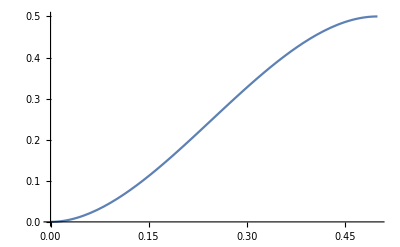

```mathematica
Plot[f[x]/.%47,{x,0,0.5}]
```

```mathematica
NDSolve[{f''''[x]==f''[x]/(x(1-x))+(2x-1)/(x^2(1-x)^2)f'[x]+(2(3 x^2-3x+1))/(x^3(1-x)^3)f[x],f[0]==0,f[0.5]==0.5,f''[0]==0,f'[0]==0},f[x],{x,0,0.5}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve::berr: The scaled boundary value residual error of 1.6297×10^11 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::ndsz: At x == 2.56163×10^-15, step size is effectively zero; singularity or stiff system suspected.

```mathematica
{{f[x]->                                  -15
InterpolatingFunction[{{2.56163 10   , 0.5}}, <>][x]}}
```

General::noinfo: Input expression                                   -15
InterpolatingFunction[{{2.56163 10   , 0.5}}, <>] contains insufficient information to interpret the result.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0000102143,0,0.0000102143}.

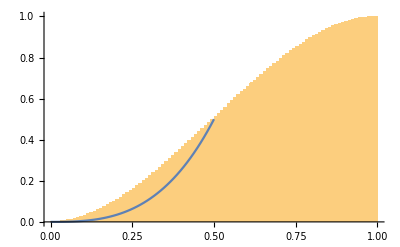

```mathematica
Show[Histogram[list,{0.01},"CDF"],Plot[1*f[x]/.%69,{x,0,0.5}]]
```

```mathematica
FindDistribution[list]
```

BetaDistribution[1.68984,1.72566]

```mathematica
list
```

{0.431654,0.671156,0.80099,0.335691,0.707706,99990,0.676654,0.721644,0.317891,0.721742,0.166646}
 |  |  |  |

```mathematica
h[x_]:=f[x]/.%45;
```

```mathematica
h'[x]
```

{f'[x]}

```mathematica
DSolve[{f''''[x]==f''[x]/(x(1-x))+(2x-1)/(x^2(1-x)^2)f'[x]+(2(3 x^2-3x+1))/(x^3(1-x)^3)f[x],f[0]==0,f[0.5]==0.5,f'[0.5]==0,f'[0]==0},f[x],x]
```

DSolve[{f^(4)[x]==(2 (1-3 x+3 x^2) f[x])/((1-x)^3 x^3)+((-1+2 x) f'[x])/((1-x)^2 x^2)+f''[x]/((1-x) x),f[0]==0,f[0.5]==0.5,f'[0.5]==0,f'[0]==0},f[x],x]

```mathematica
PDF[BetaDistribution[1.689840050375604,1.7256585353319343],x]
```

Piecewise[{{3.65841 (1-x)^0.725659 x^0.68984, 0<x<1}, {0, True}}]

```mathematica
f[x_]:=Integrate[3.65840959723044 (1-x)^0.7256585353319343 x^0.6898400503756039,{x,0,x}];
x^2+1/2 Integrate[f[x],{x,0,1}]-Integrate[Integrate[L*f[x],{x,x/L,1}],{L,x,1}]-Integrate[Integrate[L*f[x],{x,0,(x+L-1)/L}],{L,1-x,1}]/.x->0.5
```

Integrate::pwrl: Unable to prove that integration limits {1,x/L} are real. Adding assumptions may help.

Integrate::pwrl: Unable to prove that integration limits {0,(-1+L+x)/L} are real. Adding assumptions may help.

Integrate::ilim: Invalid integration variable or limit(s) in {0.5,0,1}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.5,0,(-0.5+L)/L}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.5,0.5/L,1}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

0.25+1/2 ∫_0^1 0.508742ⅆ0.5-∫_0.5^1 (∫_0^((-0.5+L)/L) 0.508742 Lⅆ0.5)ⅆL-∫_0.5^1 (∫_(0.5/L)^1 0.508742 Lⅆ0.5)ⅆL

```mathematica
3.65840959723044 (1-x)^0.7256585353319343 x^0.6898400503756039
```

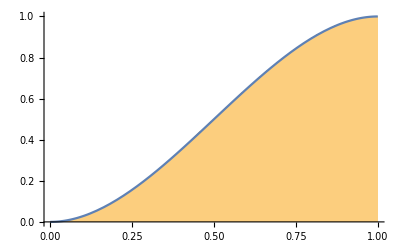

```mathematica
Show[Histogram[list,{0.001},"CDF"],Plot[Integrate[6x(1-x),{x,0,a}],{a,0,1}]]
```

————————————————————————————

```mathematica
3.35 4.6 7 9 11 13
```

```mathematica
3.35
```

```mathematica
M(x)dx=3 x^2 dx
N(x)dx=2a(1-a)+1-a^2
```

```mathematica
Simplify[2a(1-a)+1-a^2]
```

1+2 a-3 a^2

```mathematica
Integrate[%,{a,0,1}]
```

1

```mathematica
Show[Plot3D[2y,{x,0,1},{y,0,1}],ContourPlot3D[{x==0.3,y==0.3,y==x},{x,0,1},{y,0,1},{z,0,2}]]
```

-Graphics3D-

```mathematica
4.6
```

```mathematica
Integrate[2*E^(-2x)*x,{x,0,Infinity}]
```

1/2

```mathematica
Integrate[2*E^(-2x)*(3x-1),{x,0,Infinity}]
```

1/2

```mathematica
Integrate[Integrate[2/x*E^(-2x)*x*y,{y,0,x}],{x,0,Infinity}]
```

1/4

```mathematica
7.
```

```mathematica
Simplify[(1-x/2)*x+(1/2+x/2)*(1-x)]
```

1/2+x-x^2

```mathematica
Solve[D[%,x]==0,x]
```

{{x→1/2}}

```mathematica
9.
```

```mathematica
FullSimplify[((1-z)^y*1+(1-(1-z)^y)*y)*x/y]
```

x-(x (-1+y) (1-z)^y)/y

```mathematica
Solve[D[FullSimplify[((1-z)^y*1+(1-(1-z)^y)*y)*1/y],y]==0,y]
```

{{y→(-√(-4+Log[1-z]) √Log[1-z]+Log[1-z])/(2 Log[1-z])},{y→(√(-4+Log[1-z]) √Log[1-z]+Log[1-z])/(2 Log[1-z])}}

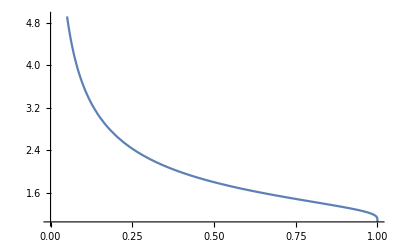

```mathematica
Plot[Select[y/.Solve[D[FullSimplify[((1-z)^y*1+(1-(1-z)^y)*y)*1/y],y]==0,y],Positive],{z,0,1}]
```

```mathematica
z=0.2;
Select[y/.Solve[D[FullSimplify[((1-z)^y*1+(1-(1-z)^y)*y)*1/y],y]==0,y],Positive]
Clear[z];
```

{2.67518}

```mathematica
11.
```

```mathematica
(1).0
(2).
```

```mathematica
Integrate[2Pi*r^2,{r,0,a}]/Integrate[2Pi r,{r,0,a}]
```

(2 a)/3

```mathematica
13.
```

```mathematica
1-2*Integrate[n*(1-x)^(n-1)*x,{x,0,1}]
```

ConditionalExpression[1-(2 n)/(n+n^2),Re[n]>0]

```mathematica
Simplify[1-(2 n)/(n+n^2)]
```

(-1+n)/(1+n)

```mathematica
Integrate[1.6*Exp[-2x],{x,0.25,Infinity}]/Integrate[1.6*Exp[-2x]+0.8*Exp[-4x],{x,0.25,Infinity}]
```

0.868332

```mathematica
Integrate[1.6*Exp[-2x]+0.8*Exp[-4x],{x,0,Infinity}]
```

1.

```mathematica
Integrate[Exp[1-y]*y,{y,1,Infinity}]
```

2

```mathematica
DistributionFitTest[list,BetaDistribution[2,2],"HypothesisTestData"]["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.842207 | 0.451551
Cramér-von Mises | 0.115626 | 0.513565
Kolmogorov-Smirnov | 0.000739057 | 0.64561
Kuiper | 0.00136257 | 0.312194
Pearson χ^2 | 464.945 | 0.880673
Watson U^2 | 0.11132 | 0.221787

```mathematica
list
```

{0.153965,0.620356,0.693585,1.80428,1.53382,99990,0.782915,1.27393,1.29695,1.23218,1.13633}
 |  |  |  |

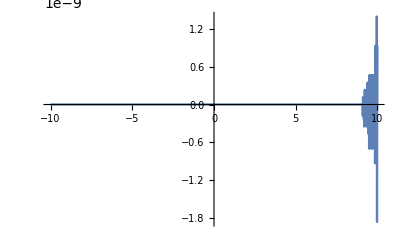

```mathematica
Plot[Chop[Gamma[x+1]-x*Gamma[x]],{x,-10,10}]
```

```mathematica
4.14
```

```mathematica
FullSimplify[Sum[PDF[PoissonDistribution[λ],x]*p^y*(1-p)^(x-y)*Binomial[x,y],{x,y,Infinity}]
]
```

Piecewise[{{(ⅇ^(-p λ) p^y λ^y)/(y!), y>0}, {(ⅇ^(-p λ) p^y λ^y (Gamma[-Floor[y]]-Gamma[-Floor[y],λ-p λ]))/(Gamma[1+y] Gamma[-Floor[y]]), True}}]

```mathematica
Sum[PDF[PoissonDistribution[p λ],x]*x,{x,0,Infinity}]
```

p λ

```mathematica
4.16
```

```mathematica
Integrate[PDF[GammaDistribution[α,1/λ],x]*x^k,{x,0,Infinity}]
```

Piecewise[{{((1/λ)^-α λ^(-k-α) Gamma[k+α])/Gamma[α], Re[λ]>0&&Re[k+α]>0}, {Integrate[x^k (Piecewise[{{(ⅇ^(-x λ) x^(-1+α) (1/λ)^-α)/Gamma[α], x>0}, {0, True}}]),{x,0,∞},Assumptions→Re[k+α]≤0||Re[λ]≤0], True}}]

```mathematica
Integrate[PDF[GammaDistribution[α,1/λ],x]*x^2,{x,0,Infinity}]-Integrate[PDF[GammaDistribution[α,1/λ],x]*x,{x,0,Infinity}]^2
```

-(Piecewise[{{((1/λ)^-α λ^(-1-α) Gamma[1+α])/Gamma[α], Re[λ]>0&&Re[α]>-1}, {Integrate[x (Piecewise[{{(ⅇ^(-x λ) x^(-1+α) (1/λ)^-α)/Gamma[α], x>0}, {0, True}}]),{x,0,∞},Assumptions→Re[α]≤-1||Re[λ]≤0], True}}])^2+(Piecewise[{{((1/λ)^-α λ^(-2-α) Gamma[2+α])/Gamma[α], Re[λ]>0&&Re[α]>-2}, {Integrate[x^2 (Piecewise[{{(ⅇ^(-x λ) x^(-1+α) (1/λ)^-α)/Gamma[α], x>0}, {0, True}}]),{x,0,∞},Assumptions→Re[α]≤-2||Re[λ]≤0], True}}])

```mathematica
Integrate[PDF[GammaDistribution[α,1/λ],x]*(x-Mean[GammaDistribution[α,1/λ]])^2,{x,0,Infinity}]
```

Piecewise[{{((1/λ)^-α λ^(-2-α) Gamma[1+α])/Gamma[α], Re[λ]>0&&Re[α]>0}, {Integrate[(x-α/λ)^2 (Piecewise[{{(ⅇ^(-x λ) x^(-1+α) (1/λ)^-α)/Gamma[α], x>0}, {0, True}}]),{x,0,∞},Assumptions→Re[α]≤0||Re[λ]≤0], True}}]

```mathematica
Variance[GammaDistribution[α,1/λ]]
```

α/λ^2

```mathematica
4.17
```

```mathematica
PDF[LaplaceDistribution[],x]
```

Piecewise[{{ⅇ^-x/2, x≥0}, {ⅇ^x/2, True}}]

```mathematica
Variance[LaplaceDistribution[]]
```

2

```mathematica
Integrate[PDF[LaplaceDistribution[],x]*x^2,{x,0,Infinity}]
```

1

```mathematica
Integrate[PDF[LaplaceDistribution[],x]*x^2,{x,0,Infinity}]-Integrate[PDF[LaplaceDistribution[],x]*x,{x,0,Infinity}]^2
```

3/4

```mathematica
4.18
```

```mathematica
(1).
```

```mathematica
0.02*0.7+0.1*0.2+0.1*0.26
```

0.06

```mathematica
Sum[Binomial[100,x]*0.06^x*0.94^(100-x)*x^2,{x,0,100}]
```

41.64

```mathematica
41.64-6^2
```

5.64

```mathematica
(2).
```

```mathematica
Sum[Binomial[100,x]*0.02^x*0.98^(100-x)*x,{x,0,100}]
```

2.

```mathematica
Sum[Binomial[100,x]*0.02^x*0.98^(100-x)*(x-2)^2,{x,0,100}]
```

1.96

```mathematica
4.19
```

```mathematica
(1).
```

```mathematica
3/4
```

```mathematica
(2).0;0.5
```

```mathematica
Tan[2*6^(1/2)]x/5+ArcTan[2*6^(1/2)]
```

ArcTan[2 √6]+1/5 x Tan[2 √6]

```mathematica
Solve[Tan[2/5 Sqrt[6]*x+ArcTan[2Sqrt[6]]]==2Sqrt[6],x]
```

{{x→ConditionalExpression[(5 π C[1])/(2 √6),C[1]∈Integers]}}

```mathematica
N[(5 π C[1])/(2 √6)]/.C[1]->1
```

3.20637

```mathematica
22.
```

```mathematica
(1).
```

```mathematica
Integrate[1/4(1+x*y)*Boole[Abs[x]<1&&Abs[y]<1],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1

```mathematica
Integrate[1/4(1+x*y)*Boole[Abs[x]<1&&Abs[y]<1]*x*y,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1/9

```mathematica
Integrate[1/4(1+x*y)*Boole[Abs[x]<1&&Abs[y]<1]*x^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1/3

```mathematica
Integrate[1/4(1+x*y)*Boole[Abs[x]<1&&Abs[y]<1]*(x^2-1/3)(y^2-1/3),{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

0

```mathematica
26.
```

```mathematica
(1).
```

```mathematica
f=p*PDF[NormalDistribution[0,1],x]+(1-p)*PDF[NormalDistribution[0,1],-x]
```

```mathematica
(2)
```

```mathematica
Integrate[p*PDF[NormalDistribution[0,1],x]*x^2-(1-p)*PDF[NormalDistribution[0,1],-x]*x^2,{x,-Infinity,Infinity}]
```

-1+2 p

```mathematica
Variance[NormalDistribution[0,1]]
```

1

```mathematica
27.
```

```mathematica
TableForm[{{2/5,1/5},{1/5,1/5}},TableHeadings->{{"X=0","X=1"},{"Y=0","Y=1"}}]
```

| Y=0 | Y=1
X=0 | 2/5 | 1/5
X=1 | 1/5 | 1/5

```mathematica
1/3*2/5*1/3-1/3*2/3*1/5*2+2/3*1/5*2/3
```

2/45

```mathematica
29.
```

```mathematica
(1).
```

```mathematica
PDF[MultinormalDistribution[{0,0,1},{{1,2,-1},{2,16,0},{-1,0,4}}],{x1,x2,x3}]
```

ⅇ^(1/2 (-x2 (-x1/4+(3 x2)/32+(1-x3)/16)-x1 (2 x1-x2/4+1/2 (-1+x3))-(x1/2-x2/16+3/8 (-1+x3)) (-1+x3)))/(16 π^(3/2))

```mathematica
Integrate[PDF[MultinormalDistribution[{0,0,1},{{1,2,-1},{2,16,0},{-1,0,4}}],{x1,x2,x3}],{#1,-Infinity,Infinity},{#2,-Infinity,Infinity}]&@@@Tuples[{x1,x2,x3},2]
```

{ⅇ^(ⅈ Im[-x2^2/32-1/8 (-1+x3)^2]) ∞,(ⅇ^(-1/8 (-1+x3)^2))/(2 √(2 π)),(ⅇ^(-x2^2/32))/(4 √(2 π)),(ⅇ^(-1/8 (-1+x3)^2))/(2 √(2 π)),ⅇ^(-1/6 ⅈ Im[4 x1^2+2 x1 (-1+x3)+(-1+x3)^2]) ∞,(ⅇ^(-x1^2/2))/(√(2 π)),(ⅇ^(-x2^2/32))/(4 √(2 π)),(ⅇ^(-x1^2/2))/(√(2 π)),ⅇ^(-1/24 ⅈ Im[16 x1^2-4 x1 x2+x2^2]) ∞}

```mathematica
Correlation[MultinormalDistribution[{0,0,1},{{1,2,-1},{2,16,0},{-1,0,4}}]]//TableForm
```

1 | 1/2 | -1/2
1/2 | 1 | 0
-1/2 | 0 | 1

```mathematica
Integrate[PDF[MultinormalDistribution[{0,0,1},{{1,2,-1},{2,16,0},{-1,0,4}}],{x1,x2,x3}],{x1,-Infinity,Infinity}]
```

(ⅇ^(-x2^2/32-1/8 (-1+x3)^2))/(16 π)

```mathematica
x1=x3-y2,x2=x1-y1=x3-y2-y1
```

```mathematica
Integrate[PDF[MultinormalDistribution[{0,0,1},{{1,2,-1},{2,16,0},{-1,0,4}}],{x1,x2,x3}]/.{x1->x3-y2,x2->x3-y2-y1},{x3,-Infinity,Infinity}]
```

(ⅇ^(-y1^2/26-1/14 (-1+y2)^2))/(2 √91 π)

```mathematica
30.
```

```mathematica
Integrate[PDF[MultinormalDistribution[Table[1.5,30],DiagonalMatrix[Table[0.1^2,30]]],Table[A[i],{i,1,30}]]*Boole[Total[Table[A[i],{i,1,30}]]>46],##]&@@Table[{A[i],-Infinity,Infinity},{i,1,30}]
```

$Aborted

```mathematica
Apply[NIntegrate[PDF[MultinormalDistribution[Table[1.5,30],DiagonalMatrix[Table[0.1^2,30]]],Table[A[i],{i,1,30}]]*Boole[Total[Table[A[i],{i,1,30}]]>46],##]&,Table[{A[i],-Infinity,Infinity},{i,1,30}]]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.

```mathematica
f[a,Table[{A[i],-Infinity,Infinity},{i,1,30}]]
```

f[a,{{A[1],-∞,∞},{A[2],-∞,∞},{A[3],-∞,∞},{A[4],-∞,∞},{A[5],-∞,∞},{A[6],-∞,∞},{A[7],-∞,∞},{A[8],-∞,∞},{A[9],-∞,∞},{A[10],-∞,∞},{A[11],-∞,∞},{A[12],-∞,∞},{A[13],-∞,∞},{A[14],-∞,∞},{A[15],-∞,∞},{A[16],-∞,∞},{A[17],-∞,∞},{A[18],-∞,∞},{A[19],-∞,∞},{A[20],-∞,∞},{A[21],-∞,∞},{A[22],-∞,∞},{A[23],-∞,∞},{A[24],-∞,∞},{A[25],-∞,∞},{A[26],-∞,∞},{A[27],-∞,∞},{A[28],-∞,∞},{A[29],-∞,∞},{A[30],-∞,∞}}]

```mathematica
Fold[Integrate[PDF[MultinormalDistribution[Table[1.5,30],DiagonalMatrix[Table[0.1^2,30]]],Table[A[i],{i,1,30}]]*Boole[Total[Table[A[i],{i,1,30}]]>46],{#,-Infinity,Infinity}]&,Table[A[i],{i,1,30}]]
```

Integrate::ilim: Invalid integration variable or limit(s) in {-(5.32442×10^16 ⅇ^(«1») (-2.50663 √((-89.+«28»+Times[«2»])^2)+«59»))/(√((-89.+2. A[2]+2. A[3]+«25»+2. A[29]+2. A[30])^2)),-∞,∞}.

Integrate::idiv: Integral of 1.06488×10^18 ⅇ^(1/2 («1»)) Boole[A[1]+A[2]+A[3]+A[4]+A[5]+A[6]+A[7]+A[8]+A[9]+A[10]+A[11]+A[12]+A[13]+A[14]+A[15]+A[16]+A[17]+A[18]+A[19]+A[20]+A[21]+A[22]+A[23]+A[24]+A[25]+A[26]+A[27]+A[28]+A[29]+A[30]>46] does not converge on {-∞,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

∫_(-∞)^∞ 1.06488×10^18 ⅇ^1 Boole[A[1]+A[2]+A[3]+A[4]+A[5]+A[6]+A[7]+A[8]+A[9]+A[10]+A[11]+A[12]+A[13]+4+A[18]+A[19]+A[20]+A[21]+A[22]+A[23]+A[24]+A[25]+A[26]+A[27]+A[28]+A[29]+A[30]>46]ⅆ(∫_1^∞ 1)
 |  |  |  |

```mathematica
Apply[f,{{1},{2}}]
```

f[{1},{2}]

```mathematica
Apply[f[#]&,Table[{A[i],-Infinity,Infinity},{i,1,30}]]
```

f[{A[1],-∞,∞}]

```mathematica
Integrate[PDF[NormalDistribution[1.5*30,Sqrt[0.1^2*30]],x],{x,46,Infinity}]
```

0.0339446-8.26637×10^-13 ⅈ

```mathematica
Integrate[1/4(1+x y),{y,-1,1}]
```

1/2

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[55*0.1,Sqrt[0.032^2*55]],x],{x,-Infinity,6}]
```

0.982436

```mathematica
Integrate[PDF[NormalDistribution[55*0.1,0.032],x],{x,6,Infinity}]
```

7.27575×10^-12-3.61773×10^-12 ⅈ

```mathematica
PDF[NormalDistribution[1.5*30,Sqrt[0.1^2*30]],x]
```

0.728366 ⅇ^(-1.66667 (-45.+x)^2)

```mathematica
PDF[NormalDistribution[a,b],x]
```

(ⅇ^(-(-a+x)^2/(2 b^2)))/(b √(2 π))

```mathematica
100/5.6
```

17.8571

————————————————————————————————————

```mathematica
2.6.7.11
```

```mathematica
2.
```

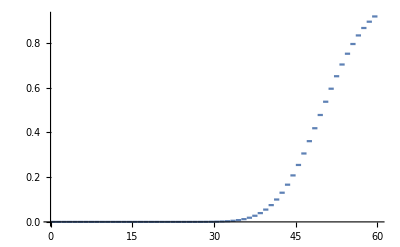

```mathematica
Plot[CDF[BinomialDistribution[500,0.1],x],{x,0,60}]
```

```mathematica
NIntegrate[PDF[BinomialDistribution[500,0.1],x],{x,0,500}]
```

1.

```mathematica
Variance[BernoulliDistribution[0.1]]
```

0.09

```mathematica
Mean[BernoulliDistribution[0.1]]
```

0.1

```mathematica
(0.09/500)/(0.05)^2
```

0.072

```mathematica
1-%
```

0.928

```mathematica
6.
```

```mathematica
Table[Total[#]/Total[#^2]&@RandomVariate[NormalDistribution[],1000000],3]
```

{0.00190525,0.00193625,0.00106723}

```mathematica
Integrate[PDF[ExponentialDistribution[1/λ],x]*x^2,{x,0,Infinity}]
```

Piecewise[{{2 λ^2, Re[λ]>0}, {Integrate[x^2 (Piecewise[{{ⅇ^(-x/λ)/λ, x≥0}, {0, True}}]),{x,0,∞},Assumptions→Re[λ]≤0], True}}]

```mathematica
7.
```

```mathematica
Mean[ExponentialDistribution[1/λ]]
```

λ

```mathematica
StandardDeviation[ExponentialDistribution[λ]]
```

1/λ

```mathematica
(a/50-2λ)/(5λ)->NormalDistribution[]
```

```mathematica
N[2λ,25 λ^2]
```

```mathematica
Integrate[PDF[NormalDistribution[],x],{x,-Infinity,(2/λ^2-1/λ)/(10/λ)}]//Simplify
```

1/2 Erfc[(-2+λ)/(10 √2 λ)]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
11.
```

```mathematica
StandardDeviation[BernoulliDistribution[0.7]]
```

0.458258

```mathematica
(1/100 Sum[X_i,{i,1,100}]-0.7)/(0.458258/Sqrt[100])~N[0,1]
```

```mathematica
CDF[NormalDistribution[],(0.7-0.7)/(0.458258/Sqrt[100])]
```

0.5

```mathematica
FindDistribution[If[#>0.8,0,If[#>0.64,1,If[#>0.8^3,2,4]]]&/@RandomReal[{0,1},100000]]
```

DataDistribution[…]

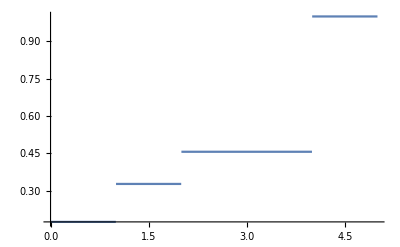

```mathematica
Plot[CDF[%44,x],{x,0,5}]
```

```mathematica
If[#>0.8,0,If[#>0.64,1,If[#>0.8^3,2,4]]]&/@RandomReal[{0,1},10000]
```

```mathematica
Mean[%44]
```

2.58278

```mathematica
Variance[%44]
```

2.68686

```mathematica
0.2*0+0.16*1+0.64*0.8*4+(1-0.2-0.16-0.8*0.64)*2
```

2.464

```mathematica
0.2*2.464^2+0.16*1.464^2+0.64*0.8*(4-2.464)^2+(1-0.2-0.16-0.8*0.64)*0.464^2
```

2.7927

```mathematica
CDF[NormalDistribution[],(a/100-2.464)/(Sqrt[2.7927]/10)]/.a->220
```

0.0570806

```mathematica
1-%
```

0.942919

```mathematica
CharacteristicFunction[BetaDistribution[a,a],x]
```

Hypergeometric1F1[a,2 a,ⅈ x]

```mathematica
7.9.10.11.12
```

```mathematica
7.
```

```mathematica
X̄~N[μ,σ^2/9]
```

```mathematica
Mean[ChiSquareDistribution[4]]
```

4

```mathematica
Variance[ExponentialDistribution[λ]]
```

1/λ^2

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
Integrate[10#*(1-#)^9,{x,0,Infinity}]&[PDF[ExponentialDistribution[λ],x]]
```

Piecewise[{{-(-2+λ) (5-10 λ+10 λ^2-5 λ^3+λ^4) (1-2 λ+4 λ^2-3 λ^3+λ^4), Re[λ]>0}, {Integrate[10 (1-(Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]))^9 (Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]),{x,0,∞},Assumptions→Re[λ]≤0], True}}]

```mathematica
Integrate[PDF[ExponentialDistribution[λ],a],{a,x,Infinity},Assumptions->x>0]
```

Piecewise[{{ⅇ^(-x λ), x>0&&Re[λ]>0}, {Integrate[Piecewise[{{ⅇ^(-a λ) λ, a≥0}, {0, True}}],{a,x,∞},Assumptions→x>0&&Re[λ]≤0], True}}]

```mathematica
Mean[ExponentialDistribution[10λ]]
```

1/(10 λ)

```mathematica
Variance[UniformDistribution[{0,θ}]]
```

θ^2/12

```mathematica
3.
```

```mathematica
Reduce[(n1+2n2)/(n0+n1+n2)==3/2(1-θ),θ]
```

n0+n1+n2≠0&&θ==(3 n0+n1-n2)/(3 (n0+n1+n2))

```mathematica
(3 n0+n1-n2)/(3 (n0+n1+n2))/.{n0->4,n1->3,n2->3}
```

2/5

```mathematica
Solve[D[θ^4((1-θ)/2)^8,θ]==0,θ]
```

{{θ→0},{θ→0},{θ→0},{θ→1/3},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1}}

```mathematica
Solve[D[θ^n0((1-θ)/2)^(n1+n2),θ]==0,θ]
```

{{θ→n0/(n0+n1+n2)}}

```mathematica
Solve[Mean@TransformedDistribution[x+y,{x\[Distributed]BernoulliDistribution[1-θ],y\[Distributed]BernoulliDistribution[1-θ]}]==(n1+2n2)/(n0+n1+n2),θ]
```

{{θ→(2 n0+n1)/(2 (n0+n1+n2))}}

```mathematica
(2 n0+n1)/(2 (n0+n1+n2))/.{n0->4,n1->3,n2->3}
```

11/20

```mathematica
Solve[D[θ^8*(1-θ)^6*2^3*(1-θ)^3 θ^3,θ]==0,θ]
```

{{θ→0},{θ→0},{θ→0},{θ→0},{θ→0},{θ→0},{θ→0},{θ→0},{θ→0},{θ→0},{θ→11/20},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1},{θ→1}}

```mathematica
Solve[D[θ^(2n0)*(1-θ)^(2n2)*2^(2n1)*(1-θ)^n1 θ^n1,θ]==0,θ]
```

{{θ→(2 n0+n1)/(2 (n0+n1+n2))}}

```mathematica
Solve[{2-2θ-λ==(n1+2n2)/(n0+n1+n2),4-4θ-3λ==(n1+4n2)/(n0+n1+n2)},{θ,λ}]
```

{{θ→n0/(n0+n1+n2),λ→n1/(n0+n1+n2)}}

```mathematica
%/.{n0->4,n1->3,n2->3}
```

{{θ→2/5,λ→3/10}}

```mathematica
Solve[{D[(1-θ-λ)^3 λ^3 θ^4,θ]==0,D[(1-θ-λ)^3 λ^3 θ^4,λ]==0},{θ,λ}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{θ→0},{λ→0},{λ→1-θ},{θ→2/5,λ→3/10}}

```mathematica
Solve[{D[(1-θ-λ)^n2 λ^n1 θ^n0,θ]==0,D[(1-θ-λ)^n2 λ^n1 θ^n0,λ]==0},{θ,λ}]
```

{{θ→n0/(n0+n1+n2),λ→n1/(n0+n1+n2)}}

```mathematica
4.
```

```mathematica
Mean@{0.45,0.2,0.5,0.47,0.35,1.63,0.14,0.06,0.89,0.34}
```

0.503

```mathematica
Integrate[2^-a a x^(a-1)*x,{x,0,2}]
```

ConditionalExpression[(2 a)/(1+a),Re[a]>-1]

```mathematica
Solve[(2 a)/(1+a)==0.503,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.336005}}

```mathematica
Solve[D[Times@@(2^-a a x^(a-1)*x/.x->{0.45,0.2,0.5,0.47,0.35,1.63,0.14,0.06,0.89,0.34}),a]==0,a]
```

{{a→0.},{a→0.},{a→0.},{a→0.},{a→0.},{a→0.},{a→0.},{a→0.},{a→0.},{a→0.577244}}

```mathematica
FindDistributionParameters[{0.95,0.63,1.69,0.97,1.84,1.81,0.53,0.35,1.34,0.82},UniformDistribution[{a,2}],ParameterEstimator->#]&/@{"MethodOfMoments","MaximumLikelihood"}
```

{{a→0.186},{a→0.35}}

```mathematica
FindDistributionParameters[{-0.05,-0.47,0.01,-0.03,-0.18,1.65,-0.64,-1.05,0.41,-0.19},LaplaceDistribution[0,a],ParameterEstimator->#]&/@{"MethodOfMoments","MaximumLikelihood"}
```

{{a→0.484541},{a→0.468}}